# Teoría de Autómatas y Lenguajes Formales

## MC-6003 II-2021 (Maestría en Ciencias de la Computación ITCR)

Profesor: Tomás de Camino Beck, Ph.D.

tomas.decamino@gmail.com

## Proyecto Final

Andrey Arguedas Espinoza - 2020426569

Oscar Rodríguez Arroyo - 2015183005

Oscar Salazar Lizano - 2020426732

Nota : Profesor favor dar click en “Enable Dynamics” y tener en la misma carpeta del notebook el audio que se desea encriptar, en la misma se guardará el audio encriptado.

## Introducción

El encriptamiento surge con la necesidad de proteger la información cuando esta se envía y que únicamente el destinatario final sea capaz de poder descifrar o desencriptar el mensaje que se envió originalmente.
A raíz de la necesidad de solventar el problema de proteger la información, nacen dos tipos de criptografías: simétrica y asimétrica. La criptografía simétrica es más rápida a la hora de ejecutarse, consiste en tener una llave secreta compartida entre el emisor y el receptor de un determinado mensaje. La llave se va a usar con el fin de cifrar y descifrar el mensaje respectivamente. 
Por otra parte, existe la criptografía asimétrica, mejor conocida como Public Key Cryptography, en la cuál nos vamos a enfocar en más adelante. La idea principal de este tipo de criptografía es contar con dos llaves: una pública y otra privada. La llave pública es la que va a estar expuesta para todas las personas que pertenezcan al sistema de comunicación. Mientras que la llave privada es única para cada persona. Dentro de nuestro trabajo implementamos soluciones de código implementadas en Mathematica tanto de sistemas simétricos como asimétricos, así como la experimentación del uso de sistemas asimétricos (RSA) en la encriptación de media digital como audios e imágenes.

## Teoría

### Historia

Los seres humanos han utilizado por siglos la comunicación escrita tanto para mensajería como para preservación de conocimiento, junto con esto también ha venido la necesidad de guardar secretos o cierta información como confidencial, para lograr esto surge la criptografía, el término viene del griego kryptós (secreto) y  graphé (escritura) el cual se ha definido como el ámbito de las técnicas de cifrado que buscan alterar las representaciones lingüísticas de ciertos mensajes con el fin de que sean ilegibles para receptores no autorizados. La criptografía es utilizada en distintos ámbitos como el arte, ciencia y tecnología. La criptografía clásica consiste en ocultar tanto la llave criptográfica como el algoritmo por lo que era ineficiente ya que las personas debían reunirse a compartir cómo funciona el algoritmo. Con la aparición de la informática y las transacciones que se realizan por temas de seguridad la criptografía pasó a jugar un eje central en las comunicaciones, para esto la informática desarrolla mecanismos y protocolos criptográficos que doten de mayor seguridad a las redes.

En informática los principales objetivos de usar la criptografía son confidencialidad, integridad, vinculación (firma digital) y autenticación. Un sistemaa criptográfico se considera seguro si cumple con los anteriores objetivos y además un adversario con capacidades especiales no puede romper la seguridad.

### Criptografía Simétrica

Los algoritmos de criptografía simétrica utilizan la misma llave criptográfica tanto para encriptar como para decriptar, por lo que todos los usuarios del sistema la conocen (secreto compartido), mediante el uso de la llave criptográfica y un algoritmo se convierte el mensaje a un texto cifrado, luego este con la misma llave puede ser devuelto a su estado original. Este tipo de criptografía puede ser visto como el uso de cofres, supongamos que Alice quiere enviar un mensaje a Bob, ambos han acordado que la llave criptográfica es el número 4.

Primeramente, Alice escribirá el mensaje en el alfabeto que acordaron, supongamos que son las letras de la a...z. Alice escribirá la palabra “secret” y con la llave criptográfica y el algoritmo encriptará el mensaje.

									-Graphics-

Como podemos observar el mensaje ha sido encriptado a la palabra “wigvix”, a simple vista si alguien intercepta el mensaje no podría saber que significa el mensaje encriptado. Seguidamente el mensaje encriptado es enviado a Bob y este lo recibe y debe desencriptar para poder leer el mensaje original.

-Graphics-

Finalmente Bob logra desencriptar el mensaje. Como nivel de complejidad un atacante puede contar las letras de ambos mensajes y suponer que la encriptación consiste en el cambio de letras, sería cuestión de tiempo construir un algoritmo de fuerza bruta utilizando el abecedario para hacer reemplazo de letras y llegar a descifrar cómo funciona el algoritmo y de ahora en adelante poder leer todos los mensajes que Alice y Bob se envíen.

-Graphics-

Las letras subrayadas consisten en los movimientos de encriptación de la palabra “secret” con k = 4.

-Graphics-

### Criptografía Asimétrica

El sistema asimétrico usa un par de llaves, una es pública y conocida por todo los usuarios y la segunda es privada y cada usuario tiene una diferente, está llaves son generadas por el mismo sistema y cumplen requisitos para poder encriptar y decriptar. La popularidad de estos sistemas comienza a mitades de los años 70 con la introducción del algoritmo RSA, el cual es la base de múltiples soluciones hoy en día.

-Graphics-

En este tipo de sistema cualquier persona puede encriptar con la llave pública, pero solo es posible decriptar con la privada. El uso de llaves privadas también ayuda en la autenticación de sistemas haciendo posibles conceptos como SSL y las firmas digitales.

-Graphics-	 -Graphics-

La mayor debilidad de estos sistemas se encuentra en la mala escogencia del algoritmos de generación de llaves, sobre todo si son números muy pequeños, en teoría todos los sistemas asimétricos pueden ser sometidos a un ataque de fuerza bruta sin embargo esto no es práctico, ejemplo en el caso de RSA, se tardarían años encontrado los factores de los números primos utilizados en este

Con el sistema asimétrico resolvemos un grave problema y es que si Alice fuera un banco tendría que guardar una llave de cada cliente para poder comunicarse con él y esto sería demasiado difícil de mantener y proteger.

-Graphics-

-Graphics-

### ¿Cómo generar un ataque a un sistema criptográfico?

Uno de los temas más importantes de la criptografía son los ataques, ya que existen personas que desean conocer el significado de los mensajes cifrados para sacar ventaja. 

Existen tres formas de romper la seguridad de un sistema criptográfico.

La primera consiste en atacar la criptografía subyacente, es decir a los mecanismos utilizados como tales, la segunda es hacer un ataque directo a la implementación, normalmente por fuerza bruta y la tercera es atacar al humano mediante presión para obtener recursos o información privilegiada.

Idealmente se busca que el sistema sea incondicionalmente seguro, esto quiere decir que aunque el atacante tenga poder computacional infinito el sistema no puede ser quebrantado. Se considera también un sistema de seguridad condicional cuando un atacante puede resolver la tarea pero no es computacionalmente factible.

AES

AES es la abreviatura de Advanced Encryption Standard y es un estándar de cifrado de Estados Unidos definido en Federal Estándar de procesamiento de información (FIPS) 192. AES es el más reciente de los cuatro algoritmos actuales aprobados por el gobierno federal de Estados Unidos. AES es un algoritmo de cifrado simétrico y procesamiento de datos en bloque de 128 bits. AES es simétrico, ya que se utiliza la misma clave para el cifrado y la transformación inversa, descifrado.

Cifrado - En el modo de cifrado, la clave inicial se agrega al valor de entrada al principio, lo que se denomina ronda inicial. Este es seguido de 9 iteraciones de una ronda normal y termina con un ronda final ligeramente modificada.Durante una ronda normal se realizan las siguientes operaciones se realiza en el siguiente orden: Sub Bytes, Shiftrows, MixColumns y AddRoundKey. La ronda final es normal sin la etapa de Mixcolumns.

-Graphics-

Subbytes: un paso de sustitución no lineal en el que cada byte se reemplaza con otro según una búsqueda en una tabla (estructura de datos).

Shiftrows: un paso de transposición en el que cada fila del estado se cambia cíclicamente un cierto número de pasos.

MixColumns: una operación de mezcla que opera en las columnas del estado, combinando los cuatro bytes en cada columna.

AddRoundKey: cada byte del estado se combina con la clave; cada clave de ronda se deriva de la clave de cifrado utilizando un programa de claves.

Descifrado - En el modo de descifrado, las operaciones se realizan en orden inverso en comparación con su orden en el modo de cifrado. Por lo tanto, comienza con una ronda inicial, seguida de 9 iteraciones de una ronda normal inversa y termina con una AddRoundKey. Una ronda normal inversa consta de las siguientes operaciones en este orden: AddRoundKey, InvMixColumns, InvShiftRows e InvSubBytes. Una ronda inicial es una ronda normal inversa sin InvMixColumns (el prefijo Inv en cada una de las operaciones se refiere a aplicar inversamente las mismas operaciones del proceso de cifrado).

-Graphics-

Aplicaciones - El cifrado y descifrado AES tiene muchas aplicaciones. Se utiliza en los casos en que los datos son demasiado sensibles y se supone que solo las personas autorizadas deben conocer y no el resto. Las siguientes son las diversas aplicaciones:

A nivel de comunicación, 
  - Smart Cards
  - RFID
  - ATM networks
  - Image encryption

A nivel de almacenamiento, 
  - Documentos confidenciales de cooperación
  - Documentos gubernamentales
  - Archivos del FBI
  - Dispositivos de almacenamiento personal
  - Protección de la información personal

### RSA

El método de RSA (Rivest–Shamir–Adleman), es un encriptamiento asimétrico de llave pública.  El primer paso para encriptar utilizando el método RSA, es generar una llave. Para generar esta llave, se necesitan dos números primos (p, q), los cuáles deberían ser preferiblemente grandes, con el fin de que sean más difíciles de adivinar. Posteriormente, se genera el producto (n) de ambos números primos por medio de la siguiente fórmula:

													n = p * q

Una vez calculado el módulo (n), se necesita calcular el producto de p - 1 y q - 1 por medio de la función de Euler ‘s totient. Para esto se define la siguiente fórmula:
 
													ϕ(n)=(p−1) * (q−1)

Cuando se obtiene el valor de ϕ(n), el siguiente paso es determinar e (Encryption number) y d (Decryption number), donde e < ϕ(n) y e es coprimo con ϕ(n). Para lograr determinar cuáles números deben escogerse, se debe cumplir la siguiente fórmula:

													e*d mod ϕ(n) = 1

Una vez se conocen tanto e como d, ya se puede conocer la llave pública (e, n) y la llave privada (d, n).

-Graphics-

### Complejidad NP de RSA

La fuerza del algoritmo RSA consta en que sería muy difícil encontrar los 2 factores p y q del número N, que esto serviría para poder obtener los valores de decriptado. Por ejemplo, supongamos que un usuario solo conoce la llave pública la cual es {5,14}. El número 14 es el N y el 5 es el e. Si se quisiera obtener la llave privada se necesita hacer lo siguiente:

Supongamos que tenemos un programa que nos da los factores de N, este nos devuelve p y q, tal que N = p * q.

{p,q} = factores(N);

Luego definimos T como :

T = (p - 1) * (q - 1);

Con p y q podemos obtener la llave privada haciendo : 

decrypt = PowerMod[e,-1,T];

Finalmente la llave privada es {5,14}.

En el ejemplo anterior esto es simple debido a que los números son pequeños pero en la vida real los números que utilizamos como N son muy grandes, generalmente se usan números mayores a 200 bits.

-Graphics-

Este tipo de problemas se conocen como derivados del Subset Sum Problem y pertenecen a los problemas conocidos como NP-Complete. Por ejemplo para el Subset Sum Problem tenemos que se nos da una cantidad de números, n = 5 -> {5,8,4,6,11} y B = 20 y necesitamos dar la lista de soluciones cuyos números sumados es igual a 20. Esto lo podemos ver como un problema de bloques y debemos saber con cuales bloques se llega a la suma de 20.
								-Graphics-

A nivel de computación tendríamos que computar 2^n veces para saber si encontramos una solución.

-Graphics-

### RSA en SSL

Gracias al algoritmo RSA la conexión segura en Internet es posible con el protocolo SSL, mediante su comunicación encriptada podemos utilizar mensajería encriptada entre el cliente y el servidor.

### -Graphics-

Dentro del mismo browser podemos observar los factores de uso del RSA, por ejemplo en la pagina www.github.com

-Graphics-

Como podemos ver el algoritmo es RSA, con un N RSA-2048, el “Exponent” que observamos es nuestro número encriptador y Modulus es N, el cual si lo pasamos a decimal consiste en un número de 600 dígitos. Ahora si alguien quisiera quebrar el sistema deberá encontrar los 2 números p y q tales que N = p * q. Si los lograra encontrar podría aplicar la fórmula anteriormente vista para encontrar la clave privada. 

T = (p - 1) * (q - 1);

decrypt = PowerMod[e,-1,T];

Sin embargo, como ya sabemos encontrar p * q = N, se tardaría siglos con los mecanismos de computación actuales.

## Desarrollo de código En Mathematica y Ejemplos

##### MOST BASIC ENCRYPTION

Existen 2 personas que se comunican por mensajes encriptados, estos se ven un día en un parque y definen un numero como “public key” el cual será “4”, a partir de ahora estas personas nuncá más se volveran a ver y solamente se comunicaran por correo con los mensajes ya encriptados. Su mecanismo de encriptación funciona de la siguiente manera.

Su alfabeto es con carácteres de la “a...z”.

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

La persona A, desea enviar el mensaje “secret” a la persona B, para esto usamos el public key como la variable que nos ayudará a encriptar. El funcionamiento de nuestro algoritmo consiste en movernos “k” espacios sobre el Alfabeto para cada letra, por ejemplo con k=7 la letra “e” pasará a ser la “l”, si el algoritmo llega a la ultima letra del alfabeto debe volver a empezar

```mathematica
validateKeyRange[alphabet_, publicKey_] := Module[{},
	If[publicKey > Length[alphabet], Mod[publicKey,Length[alphabet]], publicKey]
];

encryptorDecryptor[alphabet_,message_,publicKey_]:= Module[{chars, alphabetLength, currentPositions, newPositions, newMessage,validatedKey},
alphabetLength = Length[alphabet];
validatedKey = validateKeyRange[alphabet, publicKey];
chars = Characters[message];
currentPositions = Table[Position[alphabet,i],{i, chars}] //Flatten;
newPositions = Map[If[# + validatedKey > alphabetLength, # + validatedKey - alphabetLength, If[# + validatedKey <= 0, alphabetLength + (# + validatedKey),# + validatedKey]]&,currentPositions];
newMessage = FromLetterNumber[#]& /@ newPositions;
StringJoin[newMessage]
];

encryptorDecryptor[Alphabet[],"secret",4]
```

wigvix

Como podemos observar el mensaje encriptado queda como “wigvix”, la persona B recibirá este mensaje y si alguien lo intercepta en el camino no sabrá que significa a simple vista. La persona B deberá correr el algoritmo pero con el key en negativo para decifrar el mensaje.

```mathematica
encryptorDecryptor[Alphabet[],"wigvix",-4]
```

secret

Sin embargo este método es bastante fácil de crackear, incluso si el “public key” fuese un numero muy grande, un programador nada mas mediante fuerza bruta podría probar todos los k=1...1000.... y leer cuales producen un mensaje entendible y en adelante leer todos los mensajes de estas personas.

##### RSA ALGORITHM

El metodo de encriptacion RSA se basa en la factorización de numeros primos, por ejemplo si quisieramos encontar 2 numeros que multiplicados nos den de resultado el numero “8616460799” sería sumamente dificil lograrlo manualmente, por lo que necesitamos escribir un programa para lograrlo, pero que pasaría si encontramos numeros lo suficientemente grandes como para que incluso una computadora tarde demasiado (anos) en encontrarlos.

Mediante este metodo tendremos tanto un “public key” como “private key”, y los generaremos de la siguiente manera, usando los siguientes pasos.

Paso 1 : Seleccionamos dos numeros primos en este caso serán p=2 y q=7.

```mathematica
p= 2; q=7;
```

Paso 2 : Obtenemos el producto de estos 2 numeros y lo llamaremos “N1”

```mathematica
N1 = p * q
```

14

Paso 3 : Obtenemos “T” usando Euler Totient

```mathematica
T = (p - 1) * (q - 1)
```

6

Paso 4 : Necesitamos encontrar 2 numeros “e” y “d”. que cumplan “e*d mod T = 1”. e = encryption number y d = decryption number. Para esto debemos definir ciertas reglas.

• e debe ser menor a T.

• e deber primo relativo/coprime con T

```mathematica
encryptionNumber[t1_]:= NestWhile[# - 1 &,t1 - 1,CoprimeQ]

e = encryptionNumber[T]
```

5

Paso 5 debemos encontrar “d” que cumpla “e*d mod T = 1”.

```mathematica
decryptionNumber[e1_,t1_]:= Module[{d},
	d = e1 + 1;
	While[Mod[e1 * d, t1]!= 1, Nothing; d++];
	d
];
decryptionNumber[e,T]
```

11

Habiendo obtenido el numero encriptador y el decriptador hacemos lo siguiente :

Publicamos a todos los usuarios el Public Key el cual será (e,N) = (5,14)

Guardamos nuestro Private Key el cual será (d, N) = (11,14)

```mathematica
publicKey = {5,14};
privateKey = {11,14};
```

Supongamos que ahora quiero enviar a otra persona el mensaje “b”, esta otra persona solo conoce el Public Key y tiene su propio Private Key. Para hacer el envió definimos la función de encriptado, la cual esta dada por char ^ e mod N. El resultado es 4 y lo pasamos a letras.

```mathematica
encryptDecryptMessage[message_, publicKey_] := FromLetterNumber[Mod[LetterNumber[message]^publicKey[[1]],publicKey[[2]]]];
encryptDecryptMessage["b", publicKey]
```

d

Enviamos el mensaje encriptado, y el receptor deber desencriptarlo usando char ^ d mod N

```mathematica
encryptDecryptMessage["d", privateKey]
```

b

El metodo anterior usa primos muy pequenos para construir los keys, para poder aceptar alfabetos grandes con todos los simbolos debemos hacer una mejor solución de primos, para esto tenemos los estandares RSA-#. A continuación extenderemos un poco más la funcion de encriptado y decriptado para trabajar con strings con mas simbolos.

```mathematica
p = 11777623253100600606475568688692467522395803125194264009546341998455853099782265804864870878594598047222934141798969832793441585484966407147720677990883619;
q = 12353978300203236372526910502422393557961726275268960264014521143951779860477853396347304933752339630927134439217791364721884908085632288618105974588440853;
N1 = p * q;
T = (p - 1) * (q - 1);
encrypt = encryptionNumber[T];
decrypt= PowerMod[encrypt,-1,T];
publicKey = {encrypt,N1};
privateKey = {decrypt,N1};
encryptRSA[message_, key_] := Module[{numericValue},
(* Using ASCII codes we convert to a numeric value the string *)
numericValue = FromDigits[ToCharacterCode[message], 256];
(* char ^ e mod N *)
PowerMod[numericValue, key[[1]], key[[2]]]
];
newMessage = encryptRSA["Hello I am just testing some text!", publicKey]
```

59607645092781653589099679087771742070416182499401866716863715610607712243501964550361632134740688016289300758552320975252864383432953318744156366305020329903680400614155550164031019317742819781975817233011194603370402021844816987155430618740945616946960234351300260162952953978575770419813241556230126621952

```mathematica
decryptRSA[numericEncryption_, key_] := Module[{numericValue},
(* char ^ d mod N *)
numericValue = PowerMod[numericEncryption, key[[1]], key[[2]]];
FromCharacterCode[IntegerDigits[numericValue, 256]]
];
decryptRSA[newMessage, privateKey]
```

Hello I am just testing some text!

## Experimentación y Resultados

Nuestra experimentación se basa en la utilización del algoritmo RSA para la encriptación y desencripción de media digital como audios e imágenes. Al ser media representada de distintas formas primero debimos entender como se representan los meta-datos de los audio e imagenes en Mathematica.

Primero definimos un public key y un private para poder experimentar. Además definimos donde se encuentra el archivo que deseamos encriptar y el nombre del mismo. Finalmente mostramos el audio original.

Audio Original -> C:\Users\Andrey\Desktop\Automatas\forrestGump.wav

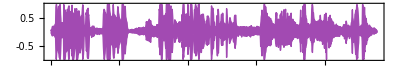

```mathematica
Nvalue = 9516311845790656153499716760847001433441357;
publicKey = {65537,Nvalue};
privateKey = {5617843187844953170308463622230283376298685,Nvalue};

(*Cambiar estos 3 valores por los datos que desee*)
directoryPath = NotebookDirectory[];
originalName = "forrestGump.wav";
encryptedName = "encrypted.wav";
(*Cambiar estos 3 valores por los datos que desee*)

audioPath = directoryPath <> originalName;
encryptedPath = directoryPath <> encryptedName;

Print["Audio Original -> ",audioPath]
audio = Audio[File[audioPath]]
AudioPlot[audio]
```

Ahora encriptaremos el audio original y podremos escuhar como suena la versión encriptada.

Encriptando el audio...

Audio encriptado creado exitosamente!

Duración de encriptado : 4.17188 segundos

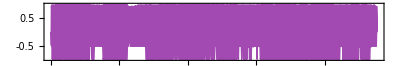

El audio encriptado ha sido exitosamente exportado -> C:\Users\Andrey\Desktop\Automatas\encrypted.wav

```mathematica
(*Obtenemos el sample rate*)
sampleRate = Import[audioPath,"SampleRate"];
(*Obtenemos los bytes del audio*)
data = AudioData[audio,"SignedInteger32"];

encryptAudio[audioData_, sampleRate_, key_] := Module[{},
(*Encriptamos los valores y tomamos el tiempo que dura*)
Timing[Map[Map[encryptRSA[ToString[#], key]&,#]&, data]]
];

Print["Encriptando el audio..."]

encryptedAudio = encryptAudio[data, sampleRate, publicKey];

Print["Audio encriptado creado exitosamente!"];
Print["Duración de encriptado : ", encryptedAudio[[1]], " segundos"];

(*Creamos un audio con los datos encriptados y lo exportamos*)
audio = Audio[ListPlay[encryptedAudio[[2]],SampleRate->sampleRate]]

AudioPlot[audio]
Export[encryptedPath,audio];
Print["El audio encriptado ha sido exitosamente exportado -> ", encryptedPath]
```

A continuación procederemos a desencriptar el audio encriptado.

Desencriptando el audio...

Duración de desencriptado : 20.4063 segundos

Audio desencriptado exitosamente!

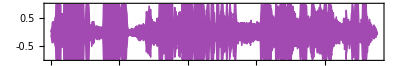

```mathematica
decryptAudio[audio_, sampleRate_, key_] := Module[{},
decrypted = Timing[Map[Map[ToExpression[decryptRSA[#, key]]&,#]&, audio]];
Print["Duración de desencriptado : ", decrypted[[1]], " segundos"];
Print["Audio desencriptado exitosamente!"];
decrypted[[2]]
];

Print["Desencriptando el audio..."];

decryptedAudio = decryptAudio[encryptedAudio[[2]], sampleRate, privateKey];

audio = Audio[ListPlay[decryptedAudio,SampleRate->sampleRate]]
AudioPlot[audio]
```

Como podemos observar, el encriptar un audio de 23 segundos nos toma aproximadamente 4 segundos, mientras que desencriptarlo tarda 21 segundos aproxiamdamente 5 veces más. Como conclusión podemos ver que gracias al uso de bytes de los audios podemos encriptarlo exitosamente.

A continuación intentaremos lo mismo pero para imagenes...

-Graphics-

Histograma de la imagen original

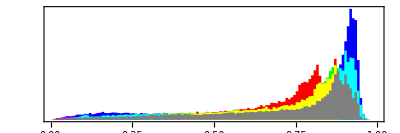

-Graphics-

Duracion del encriptamineto : 1.125 segundos

Histograma de la imagen encriptada

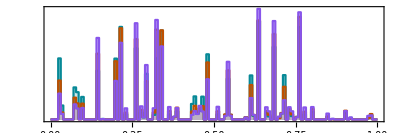

```mathematica
(* Definition of keys *)
p = 127;
q = 2;
Nvalue = p * q;
T = (p - 1) * (q - 1);
encrypt = encryptionNumber[T];
decrypt= decryptionNumber[encrypt,T];
publicKey = {encrypt,Nvalue};
privateKey = {decrypt,Nvalue};

img = Image[-Graphics-]
Print["Histograma de la imagen original"]
ImageHistogram[img]
imgData = ImageData[img,"byte"];

(*Encriptamos los valores*)
encrypted= Timing[Map[Map[Map[encryptRSA[ToString[#], publicKey]&,#]&,#]&, imgData]];

(*Mostramos la imagen encriptada*)
encryptImg = Image[encrypted[[2]], "byte"]
Print["Duracion del encriptamineto : ",encrypted[[1]], " segundos"]
Print["Histograma de la imagen encriptada"]
ImageHistogram[encryptImg]
```

Finalmente podemos ver que también es posible encriptar imagenes con el fin de añadir mas seguridad a la media digital de nuestros sistemas. Podemos observar como el histograma de la imagen cambia drásticamente en su versión encriptada.

## Comentario Final y Trabajo Futuro

Gracias a este trabajo pudimos aprender sobre la criptografía como base de múltiples soluciones en la computación actual y además logramos utilizar un algoritmo simple en soluciones más complejas. Como trabajo futuro nos hubiese gustado trabajar la encripción de videos tanto en su audio como en frames, creemos que esta aplicación podría ser utilizada en áreas como busqueda de plagio y reconocimiento de videos que incumplan leyes mediante el reconocimiento de patrones en sus bytes tanto de audio como de frames.

## Referencias

(IEEE Senior Member, Alexandria University, Egypt et al. - 2014 - Digital Image Encryption Based on RSA Algorithm.Pdf, n.d.)

Pitchaiah, M., & Daniel, P. (2012). Implementation of advanced encryption standard algorithm.

(Chandel y Patel - Image Encryption with RSA and RGB Randomized Histo.Pdf, n.d.)

Binay Kumar Singh & Sudhir Kumar Gupta. (2015). Grid-based Image Encryption using RSA.

More, S., & Bansode, R. (2015). Implementation of AES with time complexity measurement for various input. Global Journal of Computer Science and Technology: E Network, Web & Security, 15(4).